```mathematica
$Path=Prepend[$Path,"G:\\HOME\\anton\\roundabout"];
```

```mathematica
<<ACPackages`
```

```mathematica
SetWorkDir[""]
```

D:\Programs\icmm\tor2D

```mathematica
SetDirectory["d:\\home\\anton\\programs\\tor2d\\tor\\Debug"]
```

d:\home\anton\programs\tor2d\tor\Debug

```mathematica
SetWorkDir["2015.02.23\\1"]
```

D:\Programs\icmm\tor2D\2015.02.23\1

```mathematica
AverageTimeProfil[l_List,t_,dt_:1]:=Apply[Plus,#]/Length[#]&[Map[#[[2]]&,Select[lv,(t≤#[[1]][[1]]<t+dt)&]]];
UnsortedUnion[x_,ndig_:4]:=N[Reap[Sow[1,Round[10^ndig x]],_,#1&]⟦2⟧10^-ndig];
```

### Разбор логов

```mathematica
text=Import["message1.dat","Text"];
```

```mathematica
StrMsg[msg_String]:="(?s)(message of proc#(\\d+) at )?t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>msg
StrChg[par_String]:=StrMsg[par<>" was changed to"]
```

```mathematica
StrChg[par_String]:="t=(-?\\d+(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=\\d+(\\.\\d+)? sec:\\s*"<>par<>" was changed to";
```

```mathematica
Ret=StringCases[text,RegularExpression[StrChg["Re"]]:>ToExpression["$3"]]
```

```mathematica
StringCases[text,RegularExpression[StrMsg["(.*?)"]]:>"$0"]//Length
```

```mathematica
StringCases[text,RegularExpression[StrChg["rc"]]:>"$3"]
```

```mathematica
cs=StringCases[text,RegularExpression[StringJoin["(?s)(",StrChg["rc"],")?(.+?)(?=(",StrChg["rc"],")|$)"]]:>"$0"];cs={StringCases[#,RegularExpression[StrChg["rc"]]->"$3"],StringCases[#,RegularExpression[StrChg["Re"]]->"$3"],StringCases[#,RegularExpression[StrChg["omega"]]->"$3"],StringCases[#,RegularExpression[StrMsg["snap is done"]]->"$5"]}&/@cs;
TableForm[{#⟦1⟧,#⟦2⟧,#[[3]],{#⟦4⟧}}&/@cs]
```

```mathematica
cs[[1,1]]={"0.5"};cs[[1,2]]={"1.00000"};
```

```mathematica
cs[[1,1]]={"0.0"};
```

```mathematica
cs=Most[cs]
```

```mathematica
ListPlot[ToExpression/@cs[[2,2]]]
```

```mathematica
fins={ToExpression@#[[1,1]],ToExpression@Last[#[[2]]],ToExpression@Last[#[[3]]],ToExpression@Last[#[[4]]]}&/@Select[cs,Last[#]≠{}&]
```

{{0.5,1.,-0.6,130174},{0.5,1.,-0.5,134662},{0.5,1.,-0.4,227942},{0.5,1.,-0.3,166877},{0.5,1.,-0.2,149164},{0.5,1.,-0.1,144389},{0.95,0.725,-0.2,147408},{0.95,0.725,-0.3,157889},{0.95,0.725,-0.4,161295},{0.95,0.725,-0.5,169961},{0.95,0.725,-0.6,161321},{0.95,0.725,-0.7,152387},{0.95,0.725,-0.1,144389},{0.01,7.,-0.1,106204},{0.01,7.,-0.2,106407},{0.01,7.,-0.3,106614},{0.01,7.,-0.4,106860},{0.01,7.,-0.5,106986},{0.01,7.,-0.6,107317},{0.01,7.,-0.7,107673},{0.5,10.,-0.01,165868},{0.5,10.,-0.015,164913},{0.5,10.,-0.02,169399},{0.5,10.,-0.025,168443},{0.5,10.,-0.03,165305},{0.5,10.,-0.035,171249}}

```mathematica
fins=StringCases[text,RegularExpression["t=(\\d*100(\\.\\d+)?)\\s*Niter=(\\d+)\\s*time of work=(\\d+(\\.\\d+)?) sec:\nsnap is done"]:>{"$1","$3","$4"}]
```

```mathematica
StringReplace[StringDrop["="<>StringJoin[#<>"+"&/@Transpose[fins][[2]]],-1],"."->","]
```

```mathematica
ListPlot[Ret,PlotRange->{10,All},PlotLabel->Last[Ret],Joined->True]
Last[Ret]
```

## Общие тенденции

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

{2517,2.60616}

```mathematica
Scan[Print[PrintRange[#,{0,0.007}]]&,CutList[WithoutFict[#[[2]],3]&/@lv,20]]
```

```mathematica
ListPlot[{First[#],Max[WithoutFict@Last[#]]}&/@lv]
```

```mathematica
Export["energy0.dat",Transpose@Join[{ltm},len⟦All,2⟧,Map[Last,{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz},{2}]]]
```

```mathematica
Export["energy0.dat",Transpose[len]]
```

energy0.dat

```mathematica
Dimensions/@{ltm,len,mp}
```

{{78394},{14,78394},{78394,2}}

```mathematica
FileNames["en*"]
```

Import["en.zip", "energy.dat", "Elements" -> "Table"]
Import["energy.dat", "Table"]

```mathematica
len=Transpose[Fold[If[#2⟦1⟧>#1⟦-1,1⟧,Append[#1,#2],#1]&,{First[Transpose[len]]},Transpose[len]]];
```

```mathematica
Dynamic[Refresh[{
len=Transpose[Select[Import["energy.dat","Table"],0<First[#]&]];
ltm=First[len];
PrintRange[dif[Union[ltm]],All,PlotLabel->{20Length[ltm],Last[ltm]}],
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz}=Union[Transpose[{ltm,#}]]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(qvx+qvy+qvz),All,PlotLabel->√((qvx+qvy+qvz)⟦-1,-1⟧)]}
,UpdateInterval->5]]
```

```mathematica
len1=Import["energy.dat","Table"];Length[len1]
```

```mathematica
len=Transpose[Select[len1,0<First[#]&]];
ltm=First[len];PrintRange[Smooth@dif[Union[ltm]],All,PlotLabel->{100Length[ltm],Last[ltm]}]
{mp,mdp,mvx,mdvx,mvy,mdvy,mvz,mdvz,qp,qvx,qvy,qvz}=Union[Transpose[{ltm,#}]]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,Log[10,#⟦2⟧]}&/@(qvx+qvy+qvz),Automatic,PlotLabel->√((qvx+qvy+qvz)⟦-1,-1⟧)]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[{#⟦1⟧,10^Log[10,#⟦2⟧]}&,{mvx,mvy,mvz,mp},{2}],{"Maximum of vr","Maximum of vϕ","Maximum of vz","Maximum of p"}}]
```

```mathematica
Smooth[l_,part_:0.02]:=MovingAverage[l,⌈part Length[l]⌉]
```

```mathematica
ListLogPlot[dif@Smooth@mvy]
```

```mathematica
ListLimit[Take[mvy,-Min[⌊(Length[mvy]-First[Ordering[Last/@(dif@Smooth@mvy),50]])/3⌋,Length[mvy]]]//Smooth,CutValues->False,UseShift->True,ApproximationReport->{MaxError,HoelderError,LimitPlot,PolynomDegree}]
```

```mathematica
ListPlot[{1/(First[#]-685),Last[#]}&/@Take[mvy,-1000],PlotRange->{{0,Automatic},All}]
```

```mathematica
ListPlot[Take[mvy,-2000]//Smooth]
```

```mathematica
{maxvx,maxvy,maxvz,mqvx,mqvy,mqvz}=ListLimit[Take[Smooth[#],-Min[500,Length[mvy]-5]],CutValues->False,UseShift->True,ApproximationReport->{MaxError,HoelderError}]&/@{mvx,mvy,mvz,qvx,qvy,qvz}
```

```mathematica
MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[10,#⟦2⟧]}&,{qvx,qvy,qvz,qp},{2}],{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[10,#⟦2⟧]}&,{mdvx,mdvy,mdvz,mdp},{2}],{"Max difference of vr","Max difference vϕ","Max difference of vz","Max difference of p"}}]
```

## Обработка массивов

## Начало

```mathematica
dump=Release[ReadList["pumpflow0.dmp",Hold[Expression]]/.{a_+E*b_->b*10^a}];
{coor,bounds}=ReadAuxFiles2D[{"coord"},ShiftVector->{0,0},ProcDistrib->{2,2},NumberOfRefs->2];
```

```mathematica
Max/@Drop[dump,6]
```

{242410.,1.3967×10^14,8.4788×10^11,1.0497×10^13,0.01,3322.2,56.909,0.35899,57.579,0.01}

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]],2,(node/.b_:>BitAnd[b,8])/8 ar,_,$Failed]]
```

```mathematica
ReadDrawSection["pumpflow(0.5).snp",Text2D,5]
```

```mathematica
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{0,0},ProcDistrib->{2,2},NumberOfRefs->2];
Print[bounds];
```

{{-1.,1.},{-1.,1.}}

```mathematica
ACPackages`ACTextSnapManipulation`Private`ghost=6;
```

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFiles2D["pumpflow",".dmp",5,PrintInfo->None];
```

```mathematica
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{0,0},ProcDistrib->{16,16},NumberOfRefs->2];
```

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow_256_3294832.snp",5,PrintInfo->Automatic];
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{0,0},ProcDistrib->{16,16},NumberOfRefs->2];
Print[bounds];
```

{16,16}

{1.4,3294832,512,512,100.}

ghost=6

{{-1.,1.},{-1.,1.}}

```mathematica
{#⟦2⟧,Last[#]}&@Union[Flatten[p]]
```

{-110.47,0}

```mathematica
Max/@{p,vx,vy,vz,nut}
```

{0,0,1.0001,0,1}

```mathematica
asim[arr1_?ArrayQ,minus_: 1]:=Block[{arr=GetInner[arr1]},
√(Mean[Flatten@(Table[arr⟦All,i⟧-minus arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]^2)]/Mean[Flatten@(arr^2)])
]
```

```mathematica
asim1[arr1_?ArrayQ,minus_: 1]:=Block[{arr=GetInner[arr1]},
√Mean[Flatten@(Table[arr⟦All,i⟧-minus arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]^2)]
]
```

```mathematica
asim2[arr1_?ArrayQ,minus_: 1]:=Block[{arr=GetInner[arr1]},
1/Max[Abs[arr]](√Mean[Flatten@(Table[arr⟦All,i⟧-minus arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]^2)])
]
```

```mathematica
{asim[#⟦2⟧],asim[#⟦3⟧],asim[#⟦4⟧,-1]}&/@{p,vx,vy,vz,nut}
```

```mathematica
Show2x[ListPlot3D[Transpose[#],PlotRange->All,DisplayFunction->Identity]&,{p,vx,vy,nut}]
```

```mathematica
Union[Flatten[nut]]
```

```mathematica
ListPlot3D[WithoutFict@Transpose[nut],PlotRange->All]
```

```mathematica
Manipulate[PrintRange[Transpose[{coor⟦1⟧,ND[vy[[All,⌊Length[Transpose[vy]]/2⌋]],order,0.02,d]}],All,PlotLabel->Length[ND[vy[[All,⌊Length[Transpose[vy]]/2⌋]],order,0.02,d]]],{order,1,5,1},{d,0,4,1}]
```

```mathematica
PrintRange[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]]
```

```mathematica
PrintRange[dif@Transpose[WithoutFict/@{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]]
```

```mathematica
shift=Chop[Block[{fi=Interpolation[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]],t$},t$/.FindRoot[fi[t$],{t$,-1,1}]]]
```

```mathematica
With[{arr=vz},{Mean[Flatten@(Table[arr⟦All,i⟧+arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]^2)],Mean[Flatten@(arr^2)]}]
```

{7.34918×10^-9,3.16576×10^-9}

```mathematica
With[{arr=vz},ListContourPlot/@{arr,Table[arr⟦All,i⟧+arr⟦All,-i⟧,{i,1,Dimensions[arr]⟦2⟧}]}]
```

```mathematica
ListContourPlot[GetInner[Transpose[vy]],PlotRange->All,Contours->40]
```

```mathematica
ListStreamPlot[Transpose[GetInner/@{vx,vz},{3,1,2}],StreamPoints->Fine]
```

```mathematica
Export["vRe=10rc=4.gif",PrintRange[Transpose[{coor[[1]],Cut3D[Cut3D[vy,2],2,35]/(coor[[1]]0+1)}],All,PlotLabel->"Angular velocity"],ImageResolution->80,ImageSize->900];
```

## Сравнения

```mathematica
{p1,vx1,vy1,vz1,nut1}=ReadTextSnapFile2D["pumpflow_1_0.snp",5,PrintInfo->None];
```

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow_1_1.snp",5,PrintInfo->None];
```

```mathematica
Max/@Abs/@({p1,vx1,vy1,vz1,nut1}-{p,vx,vy,vz,nut})
```

{1.×10^-7,1.81×10^-9,0.,1.5×10^-9,0}

```mathematica
ArrayPlot/@({p1,vx1,vy1,vz1,nut1}-{p,vx,vy,vz,nut})
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Трёхмерное пока не работающее

```mathematica
Show2x[DensityPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},DisplayFunction->Identity]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
Show2x[ContourPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotLabel->"Max="<>ToString[Max[#]]<>"; Min="<>ToString[Min[#]],Contours->20,DisplayFunction->Identity,PlotRange->All,FrameTicks->{CutList[Transpose[{Range[Length[coor⟦1⟧]],coor⟦1⟧}],10],CutList[Transpose[{Range[Length[coor⟦3⟧]],coor⟦3⟧}],10],None,None},Axes->Automatic,AxesOrigin->{1,0}]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
Show2x[Plot3D[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotRange->All,DisplayFunction->Identity]&,{vri[r,0,z],vϕi[r,0,z],vzi[r,0,z],pi[r,0,z]}];
```

```mathematica
{vxi,vyi,vzi,pi,nuti}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vxs,vys,vzs,p,nut};
```

```mathematica
Export["fieldRe=1rc=4.gif",gds,ImageResolution->80,ImageSize->900];
```

```mathematica
gds=DisplayTogetherArray[SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic],Spacings->Scaled[0.]];
```

```mathematica
Show[gds=DrawSection["pumpflow64x64x64Re=10rc=4.snp",5],DisplayFunction->$DisplayFunction]
```

```mathematica
{vxs,vys,vzs,ps,nuts}=Transpose[((node/.b_:>0/;b≠8)/8#&/@Transpose[#])]&/@{vx,vy,vz,p,nut};
```

```mathematica
ps=(node/.b_:>0/;b≠8)/8(ps-Mean[Select[Flatten[ps],#≠0&]]);
```

```mathematica
vys=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@vy),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@vys];
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

Построение графиков и анимации давления

```mathematica
dr=ReadList["debug"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
node=Clue[nm,2];
Off[Set::write];Off[General::spell1];
ReadPressure[iter_]:=Block[{i},
Clear[dumpRead,pm,p,ps];
dumpRead=ReadList["runtest1_"<>ToString[iter]<>".snp"];
{t,count,np,n1,n2,n3,Rey}=Take[dumpRead,7];dumpRead=Drop[dumpRead,7];
{vxm,vym,vzm,pm,nutm}=Transpose[Partition[dumpRead,5]];
p=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,pm,{1,2,3}]];
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
Return[√Mean[Select[Flatten[#],Positive]]&/@(ps^2)];
];
```

```mathematica
lpres=Table[PrintRange[(#-Mean[#])&@ReadPressure[niter],{-0.5,0.7},PlotLabel->niter],{niter,100,300,100}];
```

```mathematica
ldifpres=Table[PrintRange[dif[ReadPressure[niter]],{-0.5,0.5},PlotLabel->niter],{niter,100,14200,100}];
```

```mathematica
Export["pressure.gif",lpres];
```

```mathematica
dr=ReadList["node"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
(*node=Clue[nm,2];*)
node=First[nm];
```

```mathematica
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@ps];
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

Построение графиков вдоль снэпов

```mathematica
GetShift[res_?ArrayQ]:=Block[{vy},
vy=res[[3]];
Chop[Block[{fi=Interpolation[dif@Transpose[{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋]]}]],t$},t$/.FindRoot[fi[t$],{t$,-1,1}]]]
]
GetShift[fname_String]:=
GetShift[ReadTextSnapFile2D[fname,5,PrintInfo->None]];
GetShift[iter_Integer,nproc_Integer:1]:=
GetShift["pumpflow_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp"];
```

```mathematica
ReadSection[iter_,nproc_:1]:=
ReadSection["pumpflow_"<>ToString[nproc]<>"_"<>ToString[iter]<>".snp"]
ReadSection[fname_String]:=ReadTextSnapFile2D[fname,5,PrintInfo->None]
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
{nproc}=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp"]]
```

```mathematica
nums=Flatten@cs[[All,3]]
If[Length[nums]≠Length[Union[nums]],Print["Caution! There are the same snaps!!"]];
nproc=First[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp"]]
```

```mathematica
fnames=FileNames["*.snp"]
```

```mathematica
res=Most[res];
```

```mathematica
res={};Monitor[Do[AppendTo[res,GetShift[fnames[[i]]]],{i,Length[fnames]}],ListPlot[res,PlotLabel->fnames⟦i⟧]];ListPlot[res,PlotLabel->Last[res]]
```

```mathematica
res={};Monitor[Do[AppendTo[res,ReadSection[nums⟦i⟧,nproc]],{i,Length[nums]}],nums⟦i⟧];
```

```mathematica
res={};Monitor[Do[AppendTo[res,ReadSection[fnames⟦i⟧]],{i,Length[fnames]}],fnames⟦i⟧];
```

```mathematica
Monitor[Do[Export[StringReplace[fnames⟦i⟧,".snp"->"_Re"<>ToString[infos⟦i,3⟧]<>"gif"],ListContourPlot[Transpose[res⟦i,3⟧],PlotLabel->infos⟦i⟧,Contours->30],ImageResolution->80,ImageSize->600],{i,Length[res]}],i];
```

```mathematica
res0=res;
```

```mathematica
Monitor[Do[
(*res=ReadSection[nums⟦i⟧,nproc];*)
res0=res[[i]];
Export["pumpflow_v"<>ToString[nums⟦i⟧]<>".gif",ListContourPlot[GetInner[Transpose[res0⟦3⟧]],PlotLabel->"t="<>ToString[CutNumber[infos⟦i,1⟧,3]]<>"; Iter="<>ToString[nums⟦i⟧],PlotRange->All,Contours->40],ImageResolution->80,ImageSize->600];
Export["pumpflow_w"<>ToString[nums⟦i⟧]<>".gif",ListStreamPlot[Transpose[GetInner/@{res0⟦2⟧,res0⟦4⟧},{3,1,2}],StreamPoints->Fine,PlotLabel->"t="<>ToString[CutNumber[infos⟦i,1⟧,3]]<>"; Iter="<>ToString[nums⟦i⟧]],ImageResolution->80,ImageSize->600]
,{i,1,Length[nums]}],{nums⟦i⟧,infos⟦i,1⟧}];
```

```mathematica
Manipulate[ListContourPlot[Transpose[res⟦i,3⟧],PlotLabel->Prepend[infos[[i]],ToString@nums[[i]]]],{i,1,Length[res],1}]
```

```mathematica
Manipulate[ListStreamPlot[Transpose[{res⟦i,2⟧,res⟦i,4⟧},{3,1,2}],PlotLabel->(Max/@res⟦i⟧)],{i,1,Length[res],1}]
```

```mathematica
Transpose[Map[Max,Rest/@res,{2}]]//ListPlot
```

```mathematica
infos=ScanSnaps;
```

```mathematica
ListPlot[Transpose[{infos[[All,1]],GetShift/@res}],PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
ListLinePlot[Transpose[{infos⟦All,1⟧,#}]&/@Transpose[({asim[#⟦2⟧],asim[#⟦3⟧],asim[#⟦4⟧,-1]}&/@res)]]
```

```mathematica
ListLinePlot[asim1[#,1]&/@res[[All,1]]]
```

```mathematica
ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim2[arr,1]]/@res⟦All,1⟧}],PlotRange->  All]
```

```mathematica
GraphicsGrid[{MapThread[ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim[arr,#2]]/@res⟦All,#1⟧}],PlotRange->All]&,{{2,3,4},{1,1,-1}}]}]
```

```mathematica
GraphicsGrid[{MapThread[ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim1[arr,#2]]/@res⟦All,#1⟧}],PlotRange->All]&,{{2,3,4},{1,1,-1}}]}]
```

```mathematica
GraphicsGrid[{MapThread[ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim2[arr,#2]]/@res⟦All,#1⟧}],PlotRange->All]&,{{2,3,4},{1,1,-1}}]}]
```

```mathematica
MapThread[Export[pref<>"Re10"<>#1<>"rmsq.eps",ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim[arr,#3]]/@res⟦All,#2⟧}],PlotRange->All]]&,{{"vx","vy","vz"},{2,3,4},{1,1,-1}}];
MapThread[Export[pref<>"Re10"<>#1<>"rms.eps",ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim1[arr,#3]]/@res⟦All,#2⟧}],PlotRange->All]]&,{{"vx","vy","vz"},{2,3,4},{1,1,-1}}];
MapThread[Export[pref<>"Re10"<>#1<>"rmsqmax.eps",ListLinePlot[Transpose[{infos⟦All,1⟧,Function[arr,asim2[arr,#3]]/@res⟦All,#2⟧}],PlotRange->All]]&,{{"vx","vy","vz"},{2,3,4},{1,1,-1}}];
```

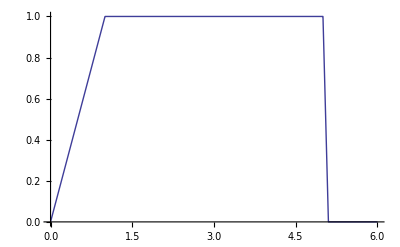

```mathematica
Plot[Which[t<1,t,1<t<5,1,5<t<5.1,1-10(t-5),t>5.1,0],{t,0,6}]
```

```mathematica
ListPlot[Transpose[{infos[[Position[infos,ToExpression[#]]⟦1,1⟧,1]]&/@nums,GetShift/@res}]]
```

```mathematica
Export["shifts.dat",Prepend[SortBy[Flatten/@Transpose[{{infos[[Position[infos,ToExpression[#]]⟦1,1⟧]],ToExpression[cs[[Position[cs,ToString[#]]⟦1,1⟧,1]]]}&/@nums,CutNumber[GetShift[#],5]&/@res}],1000#⟦4⟧+#⟦1⟧&],{"Time point","Iter","Rey","rc","Shift"}],"Table"]
```

```mathematica
Export["shifts.dat",Prepend[Sort[MapThread[{CutNumber[#1⟦1⟧,4],StringJoin@PadLeft[Characters[ToString@#1⟦2⟧],8," "],Round[#1⟦3⟧],0.45,CutNumber[#2,5]}&,{infos,GetShift/@res}]],{"Time","Iteration","Rey","rc","Shift"}],"Table"]
```

shifts.dat

```mathematica
ListLimit[Take[Transpose[{First/@SortBy[Most/@infos,Last],GetShift/@res}],{150,270}],CutValues->False,Shift->False,ApproximationReport->{LimitPlot,PolynomDegree}]
```

```mathematica
Clear[GetInflectionPoint];
GetInflectionPoint[snap_,κ_,add_String:"",viv_:True]:=Block[{nx,points},
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow_16_"<>ToString[snap]<>".snp",5,PrintInfo->None];
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{If[κ==0,0,1/κ],0},ProcDistrib->{4,4},NumberOfRefs->2];
nx=Length[coor[[1]]]-2ghost;
If[viv,Print@ListStreamPlot[Transpose[GetInner/@{vx,vz},{3,1,2}],StreamPoints->Fine,FrameLabel->"κ="<>ToString[κ]<>add,DataRange->{First@bounds,{-1,1}}];
Print[ListPlot[vx[[All,nx/2+ghost]],DataRange->{-1,1}]]];
points=Extract[(coor[[1]]-Mean@bounds[[1]])[[ghost+1;;-1-ghost]],{Pick[Range[nx-1],(Times@@#<0)&/@Partition[vx[[ghost+1;;-1-ghost,nx/2+ghost]],2,1]]}ᵀ];
If[Length[points]>1,Print["Обнаружено более одной точки смены направления течения: ",points]];
If[Length[points]<1,Print["Нет смены направления"];If[vx[[nx/2+ghost,nx/2+ghost]]>0,1,-1],Last[points]]
]
GetInflectionPointNew[κ_,R_,F_,viv_:True]:=Block[{nx,points},
{p,vx,vy,vz,nut}=ReadTextSnapFile2D["pumpflow(kappa="<>ToString@κ<>",Re="<>ToString@R<>",F="<>ToString@F<>").snp",5,PrintInfo->None];
{coor,bounds,node}=ReadAuxFiles2D[{"coord","node"},ShiftVector->{If[ToExpression@κ==0,0,1/ToExpression@κ],0},ProcDistrib->{4,4},NumberOfRefs->2];
nx=Length[coor[[1]]]-2ghost;
If[viv,Print@ListStreamPlot[Transpose[GetInner/@{vx,vz},{3,1,2}],StreamPoints->Fine,FrameLabel->"κ="<>ToString[κ]<>",Re="<>ToString@R<>",F="<>ToString@F,DataRange->{First@bounds,{-1,1}}];
Print[ListPlot[vx[[All,nx/2+ghost]],DataRange->{-1,1}]]];
points=Extract[(coor[[1]]-Mean@bounds[[1]])[[ghost+1;;-1-ghost]],{Pick[Range[nx-1],(Times@@#<0)&/@Partition[vx[[ghost+1;;-1-ghost,nx/2+ghost]],2,1]]}ᵀ];
If[Length[points]>1,Print["Обнаружено более одной точки смены направления течения: ",points]];
If[Length[points]<1,Print["Нет смены направления"];If[vx[[nx/2+ghost,nx/2+ghost]]>0,1,-1],Last[points]]
]
```

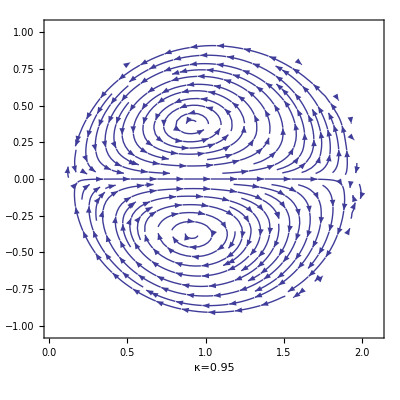

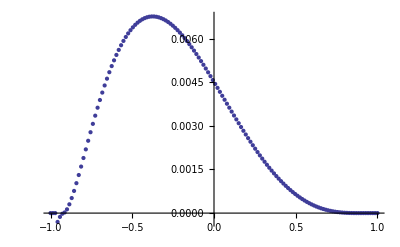

0.929688

```mathematica
GetInflectionPoint[157889,0.95]
```

```mathematica
With[{pars=Union[fins[[All,1;;2]]]},
Manipulate[ListLinePlot[Map[ToExpression,Union[{#[[1,3]],#[[2]]}&/@Select[{fins,res}ᵀ,#[[1,1;;2]]==pars[[i]]&]],{2}],AxesLabel->{"F","x_infl"},PlotLabel->"κ="<>ToString[pars⟦i,1⟧]<>"; Re="<>ToString[pars⟦i,2⟧]],{i,1,Length[pars],1}]
]
```

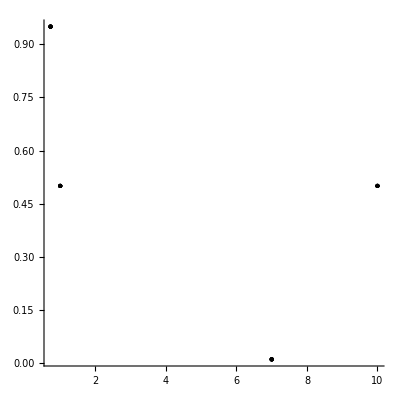

```mathematica
Graphics[Point[{#[[1,2]],#[[1,1]]}]&/@({fins,res}ᵀ),Axes->True,AspectRatio->1,AxesOrigin->{0,0}]
```

```mathematica
{#[[1,1]],#[[1,2]],#[[2]]}&/@({fins,res}ᵀ)
```

{{0.5,1.,-1},{0.5,1.,-1},{0.5,1.,-0.570313},{0.5,1.,0.273438},{0.5,1.,0.914063},{0.5,1.,1},{0.95,0.725,1},{0.95,0.725,0.929688},{0.95,0.725,0.617188},{0.95,0.725,0.351563},{0.95,0.725,0.117188},{0.95,0.725,-0.0703125},{0.95,0.725,1},{0.01,7.,-1},{0.01,7.,-1},{0.01,7.,-1},{0.01,7.,-1},{0.01,7.,-1},{0.01,7.,-1},{0.01,7.,-1},{0.5,10.,1},{0.5,10.,1},{0.5,10.,1},{0.5,10.,1},{0.5,10.,1},{0.5,10.,1}}

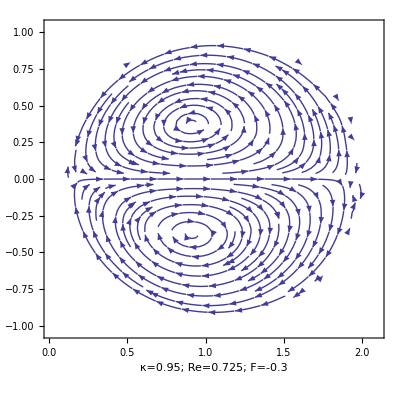

-Graphics-

```mathematica
CellPrint[Cell["Проверка на 4-вихревое течение","Section"]];
res=(CellPrint[Cell["κ="<>ToString@#[[1]]<>"; Re="<>ToString@#[[2]]<>"; F="<>ToString@#[[3]]<>"; snap="<>ToString@#[[4]],"Subsection"]];
GetInflectionPoint[#[[4]],#[[1]],"; Re="<>ToString@#[[2]]<>"; F="<>ToString@#[[3]]])&/@fins
```

```mathematica
{fins0,res0}={fins,res};
```

```mathematica
fins=
First/@StringCases[FileNames["pumpflow(*).snp"],"pumpflow(kappa="~~k__~~",Re="~~r__~~",F="~~f__~~").snp":>{k,r,f}]
```

{{0.01,7.00,-0.01},{0.01,7.00,-0.02},{0.01,7.00,-0.03},{0.01,7.00,-0.04},{0.01,7.00,-0.06},{0.01,7.00,-0.08},{0.50,10.00,-0.10},{0.50,10.00,-0.20},{0.50,10.00,-0.30},{0.50,10.00,-0.40},{0.50,1.00,-0.33},{0.50,1.00,-0.36},{0.95,0.72,-0.35},{0.95,0.72,-0.80},{0.95,0.72,-0.90},{0.95,0.72,-1.00},{0.95,7.00,-0.01},{0.95,7.00,-0.05},{0.95,7.00,-0.10},{0.95,7.00,-0.20},{0.95,7.00,-0.30}}

```mathematica
fins=Drop[fins,{4}];
```

```mathematica
GetInflectionPointNew["0.01","7.00","-0.06"]
```

```mathematica
CellPrint[Cell["Проверка на 4-вихревое течение","Section"]];
res=(CellPrint[Cell["κ="<>ToString@#[[1]]<>"; Re="<>ToString@#[[2]]<>"; F="<>ToString@#[[3]],"Subsection"]];
GetInflectionPointNew@@#)&/@fins
```

## Проверка типов ячеек

```mathematica
ghost=3;
```

```mathematica
{node,{rr,rz}}=ReadAuxFiles2D[{"node","ref"},NumberOfRefs->2,ProcDistrib->{2,2}];
```

```mathematica
Union[Flatten[node]]
```

{4,8,12,20}

```mathematica
ListDensityPlot[node]
```

```mathematica
ListDensityPlot[Transpose[BitAnd[node,8]]]
```

```mathematica
gc=Graphics[Circle[{n1/2+ghost,n1/2+ghost},n1/2]]
```

```mathematica
DisplayTogether[ListDensityPlot[node],gc];
```

```mathematica
ListDensityPlot/@{node,rr,rz};
```

```mathematica
ListContourPlot[node]
ListContourPlot[rr]
ListContourPlot[rz]
```